```mathematica
G1:=ArrayFlatten[{{PauliMatrix[1],0},{0,0}}];
G2:=ArrayFlatten[{{PauliMatrix[2],0},{0,0}}];
G3:=ArrayFlatten[{{PauliMatrix[3],0},{0,0}}];
G4:={{0,0,1},{0,0,0},{1,0,0}};
G5:={{0,0,-I},{0,0,0},{I,0,0}};
G6:={{0,0,0},{0,0,1},{0,1,0}};
G7:={{0,0,0},{0,0,-I},{0,I,0}};
G8:=1/Sqrt[3]{{1,0,0},{0,1,0},{0,0,-2}};
GM:={G1,G2,G3,G4,G5,G6,G7,G8};

VerifyGM[]:=Module[{i,j,tr},
For[i=1,i≤ Length[GM],i++,
For[j=1,j≤ Length[GM],j++,
tr=Tr[GM[[i]].GM[[j]]];
If[i==j && tr== 2,Continue[]];
If[i≠j && tr== 0,Continue[]];
Print["i=",i,",j=",j,",tr=",tr];
Return[False];
]
];

Return[True];
];

Fsu3I[a_Integer,b_Integer,c_Integer]:=0;
Fsu3I[1,2,3]:=1;
Fsu3I[1,4,7]:=1/2;
Fsu3I[1,5,6]:=-1/2;
Fsu3I[2,4,6]:=1/2;
Fsu3I[2,5,7]:=1/2;
Fsu3I[3,4,5]:=1/2;
Fsu3I[3,6,7]:=-1/2;
Fsu3I[4,5,8]:=Sqrt[3]/2;
Fsu3I[6,7,8]:=Sqrt[3]/2;

Fsu3[a_Integer,b_Integer,c_Integer]:=Module[{list},
list=Sort[{a,b,c}];
Return[Signature[{a,b,c}]*Fsu3I[list[[1]],list[[2]],list[[3]]]]
];

Fsu3Mat[a_]:=Table[Fsu3[a,i,j],{i,1,8},{j,1,8}];

Dsu3I[a_Integer,b_Integer,c_Integer]:=0;
Dsu3I[1,1,8]:=1/Sqrt[3];
Dsu3I[2,2,8]:=1/Sqrt[3];
Dsu3I[3,3,8]:=1/Sqrt[3];
Dsu3I[8,8,8]:=-1/Sqrt[3];
Dsu3I[4,4,8]:=-1/(2Sqrt[3]);
Dsu3I[5,5,8]:=-1/(2Sqrt[3]);
Dsu3I[6,6,8]:=-1/(2Sqrt[3]);
Dsu3I[7,7,8]:=-1/(2Sqrt[3]);

Dsu3I[1,4,6]:=1/2;
Dsu3I[1,5,7]:=1/2;
Dsu3I[2,4,7]:=-1/2;
Dsu3I[2,5,6]:=1/2;
Dsu3I[3,4,4]:=1/2;
Dsu3I[3,5,5]:=1/2;
Dsu3I[3,6,6]:=-1/2;
Dsu3I[3,7,7]:=-1/2;

Dsu3[a_Integer,b_Integer,c_Integer]:=Module[{list},
list=Sort[{a,b,c}];
Return[Dsu3I[list[[1]],list[[2]],list[[3]]]]
];

Dsu3Mat[a_]:=Table[Dsu3[a,i,j],{i,1,8},{j,1,8}];

VerifyFsu3[]:=Module[{i,j,k,m,res},
For[i=1,i≤ 8,i++,
For[j=1,j≤ 8,j++,
m=GM[[i]].GM[[j]]-GM[[j]].GM[[i]];
res=ConstantArray[0,{3,3}];
For[k=1,k≤ 8,k++,
res+= 2I*Fsu3[i,j,k]*GM[[k]]
];

If[Simplify[m- res]≠ ConstantArray[0,{3,3}], 
Print["i=",i, ", j=", j, ", m=",MatrixForm[m], ", res=", MatrixForm[res]]; 
Return[False]
]
]
];

Return[True]
];

VerifyDsu3[]:=Module[{i,j,k,m,res},
For[i=1,i≤ 8,i++,
For[j=1,j≤ 8,j++,
m=GM[[i]].GM[[j]]+GM[[j]].GM[[i]];
If[i==j,
res=4IdentityMatrix[3]/3,
res=ConstantArray[0,{3,3}]];
For[k=1,k≤ 8,k++,
res+= 2Dsu3[i,j,k]*GM[[k]]
];

If[m≠ res, Print["i=",i, ", j=", j]; Return[False]]
]
];

Return[True]
];

ExpF[a_List]:=Module[{mat},
mat=Sum[-a[[i]]Fsu3Mat[i],{i,1,Length[a]}];
(*Print[MatrixForm[mat]];*)
Return[MatrixExp[N[mat]]]
];

ExpGM[a_List]:=Module[{mat},
mat=Sum[I*a[[i]]GM[[i]]/2,{i,1,Length[a]}];
(*Print[MatrixForm[mat]];*)
Return[MatrixExp[N[mat]]]
];

VerifyExpF[a_List]:=Module[{i,res,v1,v2},
res=ExpF[a];
v1={};
v2={};
For[i=1,i≤ 8,i++,
AppendTo[v1,Tr[Fsu3Mat[i].res]/3];
AppendTo[v2,Tr[Dsu3Mat[i].res]*3/5];
];

res=res-Sum[v1[[i]]*Fsu3Mat[i],{i,1,8}]-Sum[v2[[i]]*Dsu3Mat[i],{i,1,8}];
Return[res]
];

VerifyTrabc[a_,b_,c_]:=Module[{act,ret},
act=Tr[GM[[a]].GM[[b]].GM[[c]]];
ret=2*(Dsu3[a,b,c]+I*Fsu3[a,b,c]);
Return[Simplify[act-ret]]
];

VerifyTrabcAll[]:=Module[{i,j,k},
For[i=1,i≤ 8,i++,
For[j=i,j≤8,j++,
For[k=j,k≤8,k++,
If[VerifyTrabc[i,j,k]≠0,
Print["VerifyTrabcAll: i,j,k=", i,",",j,",",k];
Return[False]]
]
]
];
Return[True]
];

TestTri8j8[i_,j_]:=Module[{res,exp,sigma,id},
res = Tr[GM[[i]].GM[[8]].GM[[j]].GM[[8]]+GM[[j]].GM[[8]].GM[[i]].GM[[8]]];
sigma= ConstantArray[0,{8,8}];
sigma[[8,8]]=1;
id=IdentityMatrix[8];

exp=8(sigma[[i,j]]+1/Sqrt[3]Dsu3Mat[8][[i,j]])-4/3id[[i,j]];
Return[res-exp]
];

TestTri8j3[i_,j_]:=Module[{res,exp,sigma},
res = Tr[GM[[i]].GM[[8]].GM[[j]].GM[[3]]+GM[[j]].GM[[8]].GM[[i]].GM[[3]]];
sigma= ConstantArray[0,{8,8}];
sigma[[3,8]]=1;
sigma[[8,3]]=1;
exp=4(sigma[[i,j]]-2/Sqrt[3]Dsu3Mat[3][[i,j]]);
Return[res-exp]
];

Hfun[mat_,x_]:=x^2*mat[[3,3]]+mat[[8,8]]/3-x/Sqrt[3]*(mat[[3,8]]+mat[[8,3]]);

Ffun[mat_,x_,alist_]:=Module[{exp},
exp=ExpF[alist];
Return[Hfun[exp.mat.Transpose[exp],x]]
];

TestTrUAAUB[alist_]:=Module[{A,U,Z,res,exp},
A=DiagonalMatrix[{x,-x,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.A.ConjugateTranspose[U].A];
exp=(1+2x^2)/3+2/Sqrt[3](x^2-1)(x*Z[[8,3]]-Z[[8,8]]/Sqrt[3]);
Return[res-exp]
];

(*ABABB1=(2y^2+1)/3((2x^2+1)/3+2(x^2-1)/Sqrt[3](y*Z83-Z88/Sqrt[3]));
ABABB2=(y^2-1)/(3Sqrt[3])*2/Sqrt[3]*(x^2-1)Z88;
ABABB3=(y^2-1)/Sqrt[3](-2/(9Sqrt[3])+4/(3Sqrt[3])(y(x*Z33-Z83/Sqrt[3])+1/Sqrt[3](x*Z38-Z88/Sqrt[3])));
ABABB4=(y^2-1)/Sqrt[3]*2/(3Sqrt[3])*(x^2+1/3);*)

ABABB1=(2y^2+1)/3((2x^2+1)/3+2(x^2-1)/Sqrt[3](y*Z83-Z88/Sqrt[3]));
ABABB2=(y^2-1)/Sqrt[3]*(2x^2/(3Sqrt[3])+4x*y/(3Sqrt[3])Z33);
ABABB3=(y^2-1)/Sqrt[3](4/9(x*Z38-y*Z83)+(6x^2-10)/(9Sqrt[3])Z88);
ABABB4=0;

ABABB=ABABB1+ABABB2+ABABB3+ABABB4;

cxy=Factor[ABABB/.{Z33->0,Z38->0,Z83->0,Z88->0}]
cz33=Simplify[Coefficient[ABABB,Z33]]
cz38=Simplify[Coefficient[ABABB,Z38]]
cz83=Factor[Coefficient[ABABB,Z83]]
cz88=Factor[Coefficient[ABABB,Z88]]


ClearAll[TestTrABABB];
TestTrABABB[alist_]:=Module[{A,B,U,Z,res,exp,sigma,omega},
A=DiagonalMatrix[{x,-x,1}];
B=DiagonalMatrix[{y,-y,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.ConjugateTranspose[U].B.U.A.ConjugateTranspose[U].B.B];
exp=cxy+cz33*Z[[3,3]]+cz38*Z[[3,8]]+cz83*Z[[8,3]]+cz88*Z[[8,8]];
sigma=ConstantArray[0,{8,8}];
sigma[[3,8]]=1;
sigma[[8,3]]=1;
omega=ConstantArray[0,{8,8}];
omega[[8,8]]=1;
exp+=2(y^2-1)/Sqrt[3](y*Ffun[sigma-2/Sqrt[3]*Dsu3Mat[3],x,alist]-2/Sqrt[3]Ffun[omega+Dsu3Mat[8]/Sqrt[3],x,alist]);
Print["res=",Chop[Simplify[res]]];
Return[res-exp]
];

TestTrY3[alist_]:=Module[{A,U,Z,res,exp,sigma},
A=DiagonalMatrix[{x,-x,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.ConjugateTranspose[U].GM[[8]].U.A.ConjugateTranspose[U].GM[[3]]];
sigma=ConstantArray[0,{8,8}];
sigma[[3,8]]=1;
sigma[[8,3]]=1;
exp=4/(3Sqrt[3])(x*Z[[3,3]]-Z[[8,3]]/Sqrt[3])+2Ffun[sigma-2/Sqrt[3]Dsu3Mat[3],x,alist];
Return[Chop[Collect[N[res-exp],x]]]
];

ClearAll[TestTrY8];
TestTrY8[alist_]:=Module[{A,U,Z,res,exp,omega},
A=DiagonalMatrix[{x,-x,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.ConjugateTranspose[U].GM[[8]].U.A.ConjugateTranspose[U].GM[[8]]];
omega=ConstantArray[0,{8,8}];
omega[[8,8]]=1;
exp=-2/3x^2-4/(3Sqrt[3])(x*Z[[3,8]]-Z[[8,8]]/Sqrt[3]);
exp+=4*Ffun[omega+Dsu3Mat[8]/Sqrt[3],x,alist];
Return[Chop[Collect[N[res-exp],x]]]
];

ClearAll[TestTrYB];
TestTrYB[alist_]:=Module[{A,B,U,Z,res,exp,sigma,omega},
A=DiagonalMatrix[{x,-x,1}];
B=DiagonalMatrix[{y,-y,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.ConjugateTranspose[U].GM[[8]].U.A.ConjugateTranspose[U].B];
sigma=ConstantArray[0,{8,8}];
sigma[[3,8]]=1;
sigma[[8,3]]=1;
omega=ConstantArray[0,{8,8}];
omega[[8,8]]=1;
exp=2/(3Sqrt[3])x^2+4x*y*Z[[3,3]]/(3Sqrt[3])+4/9(x*Z[[3,8]]-y*Z[[8,3]])+(6x^2-10)Z[[8,8]]/(9Sqrt[3]);
exp-=4/Sqrt[3]*Ffun[omega+Dsu3Mat[8]/Sqrt[3],x,alist];
exp+=2y*Ffun[sigma-2Dsu3Mat[3]/Sqrt[3],x,alist];
Return[Chop[Collect[N[res-exp],{x,y}]]]
];

ClearAll[TestTrUAU8UAU1];
TestTrUAU8UAU1[alist_]:=Module[{A,U,Z,res,exp,sigma},
A=DiagonalMatrix[{x,-x,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.ConjugateTranspose[U].GM[[8]].U.A.ConjugateTranspose[U]]/3;
exp=4/9(x*Z[[3,8]]-Z[[8,8]]/Sqrt[3]);
exp+=2/3*Ffun[Dsu3Mat[8],x,alist];
(*exp=2(x^2-1)/Sqrt[3]*Z[[8,8]]/3;*)
Print["res=",Chop[Simplify[res]]];
Return[res-exp]
];

ClearAll[TestTrUAU8UAU1b];
TestTrUAU8UAU1b[alist_]:=Module[{A,U,Z,res,exp,exp1},
A=DiagonalMatrix[{x,-x,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=Tr[U.A.ConjugateTranspose[U].GM[[8]].U.A.ConjugateTranspose[U]]/3;
exp1=4/3*(x*Z[[3,8]]-Z[[8,8]]/Sqrt[3]);
exp1+=2*Ffun[Dsu3Mat[8],x,alist];
exp=exp1/3;

Print["res=",Chop[Simplify[res]]];
Return[res-exp]
];

ClearAll[TestY];
TestY[alist_]:=Module[{A,U,Z,res,exp,sigma,i,j},
A=DiagonalMatrix[{x,-x,1}];
U=ExpGM[alist];
Z=ExpF[alist];
res=N[U.A.ConjugateTranspose[U].GM[[8]].U.A.ConjugateTranspose[U]];
exp=N[GM[[8]]/9+4/9*(x*Z[[3,8]]-Z[[8,8]]/Sqrt[3])*IdentityMatrix[3]];
For[i=1,i≤8,i++,
For[j=1,j≤8,j++,
exp+= 2/3*(x*Z[[3,i]]-Z[[8,i]]/Sqrt[3])*Dsu3[8,i,j]*GM[[j]];
exp+= (x*Z[[3,i]]-Z[[8,i]]/Sqrt[3])(x*Z[[3,j]]-Z[[8,j]]/Sqrt[3])*(GM[[i]].GM[[8]].GM[[j]]);
]
];

Return[N[res-exp]]
];
```

1/9 (1+2 y^2+6 x^2 y^2)

4/9 x y (-1+y^2)

(4 x (-1+y^2))/(9 √3)

(2 y (-1+3 x^2-8 y^2+6 x^2 y^2))/(9 √3)

-2/27 (-8+6 x^2-y^2+3 x^2 y^2)

```mathematica
fD3=-2/3x*Z33+1/Sqrt[3](x^2-1/3)Z83;
fD8=-2/3x*Z38+1/Sqrt[3](x^2-1/3)Z88;
fSigma=2x(x-1/Sqrt[3])Z33*Z88-2x/Sqrt[3]Z38*Z83+1/3*Z83*Z88;
fOmega=x^2Z38^2-2x/Sqrt[3]Z38*Z88+1/3*Z88^2;
tmp1=Simplify[2*(y^2-1)/3*(-2y*fD3-2/Sqrt[3]fD8)];
tmp2=Simplify[2*(y^2-1)/3(Sqrt[3]y*fSigma-2*fOmega)];

Factor[tmp/.{Z33->0,Z38->0,Z83->0,Z88->0}]+cxy;
Simplify[Coefficient[tmp1,Z33]+cz33];
Simplify[Coefficient[tmp1,Z38]+cz38];
Factor[Coefficient[tmp1,Z83]+cz83];
Factor[Coefficient[tmp1,Z88]+cz88];

tmpa=Simplify[Coefficient[tmp2,Z33*Z88]];
tmpb=Simplify[Coefficient[tmp2,Z88*Z88]];
tmpc=Simplify[Coefficient[tmp2,Z38*Z38]];
tmpd=Simplify[Coefficient[tmp2,Z38*Z88]];
tmpe=Simplify[Coefficient[tmp2,Z83*Z88]];
tmpf=Simplify[Coefficient[tmp2,Z83*Z38]];

Assert[Simplify[tmp2-(tmpa*Z33*Z88+tmpb*Z88*Z88+tmpc*Z38*Z38+tmpd*Z38*Z88+tmpe*Z83*Z88+tmpf*Z83*Z38)]==0]

trABABB=(tmp1+cxy+cz33*Z33+cz38*Z38+cz83*Z83+cz88*Z88+tmp2)

ClearAll[tmp1,tmp2,tmpa,tmpb,tmpc,tmpd,tmpe,tmpf,tmp3,tmp3a,tmp3b,z33,z33a,z33b];
```

1/9 (1+2 y^2+6 x^2 y^2)+4/9 x y (-1+y^2) Z33+(4 x (-1+y^2) Z38)/(9 √3)+(2 y (-1+3 x^2-8 y^2+6 x^2 y^2) Z83)/(9 √3)-2/27 (-8+6 x^2-y^2+3 x^2 y^2) Z88-4/27 (-1+y^2) (-2 x (3 y Z33+√3 Z38)-√3 y Z83-Z88+3 x^2 (√3 y Z83+Z88))+2/9 (-1+y^2) ((√3 y Z83-2 Z88) Z88-6 x^2 (Z38^2-√3 y Z33 Z88)+x (4 √3 Z38 Z88-6 y (Z38 Z83+Z33 Z88)))

```mathematica
(* The case that x≠ y*)
zToxy={Z38-> -Sqrt[3]y^2/(x(x^2-1)(y^4-1)), Z83->-Sqrt[3]x^2/(y(y^2-1)(x^4-1)),Z88->1+3/(y^2-1)-3x^2y^2/((x^2-1)(y^2+1))};
xyToc={x-> Sin[c],y-> Cos[c]/Sqrt[1+Sin[c]^2]};
yTox1=Table[y^(2i)->( 2/(x^2+1)-1)^i,{i,1,6}];
yTox2=Table[y^(2i+1)->y( 2/(x^2+1)-1)^i,{i,1,6}];
yTox=Join[yTox1,yTox2];

tmp3a=trABABB/.zToxy;
tmp3b=trABABB/.{Z38->Z83,Z83->Z38}/.zToxy;

tv1=Factor[Coefficient[tmp3a,Z33]];
tv2=Factor[tmp3a/.{Z33->0}];
Simplify[(1-tv2)/tv1/.yTox];
Simplify[%/.yTox];
Simplify[(y+1)(y-1)*%]/(2/(x^2+1)-2);
z33a=Simplify[%]

tv1=Factor[Coefficient[tmp3b,Z33]];
tv2=Factor[tmp3b/.{Z33->0}];
Simplify[(1-tv2)/tv1/.yTox];
Expand[%/.yTox];
Simplify[(y+1)y^3(y-1)*%]/(Expand[(y+1)y^3(y-1)]/.yTox);
z33b=Simplify[%]

Solve[z33a==z33b,y];
rooty=Factor[y/.%[[1]]]
Factor[(rooty^2+1)*(x^2+1)-2]
tmpx=Numerator[%]
NSolve[tmpx==0,x];

(*Plot[tmpx,{x,0,1}]*)
ClearAll[tmp1,tmp2,tmpa,tmpb,tmpc,tmpd,tmpe,tmpf,tmp3,tmp3a,tmp3b,z33,z33a,z33b];

(*Simplify[Z38/.zToxy/.{x->Exp[I*Pi/4],y->Exp[-I*Pi/4]}]
Simplify[Z83/.zToxy/.{x->Exp[I*Pi/4],y->Exp[-I*Pi/4]}]*)

Simplify[Z38/.zToxy/.{x->Sqrt[2]-1,y->Sqrt[2]-1}]
Simplify[Z83/.zToxy/.{x->Sqrt[2]-1,y->Sqrt[2]-1}]
N[%]
```

(3-9 x^2+13 x^4-3 x^6-24 x^8+18 x^10)/(8 (-1+x) x^3 (1+x) (3-3 √3 x+3 x^2-√3 x^3-3 x^4+3 √3 x^5) y)

(-6+6 x^2+30 x^4-72 x^6-12 x^8+84 x^10-72 x^12+18 x^14+5 x y+14 x^3 y-38 x^7 y-5 x^9 y+24 x^11 y)/(8 x^3 (-1+x^2)^3 (3-3 √3 x+3 x^2-√3 x^3-3 x^4+3 √3 x^5) y)

(9-21 x^2+4 x^4+34 x^6+7 x^8-21 x^10+12 x^12)/((-1+x)^2 x (1+x)^2 (1+x^2) (5+19 x^2+24 x^4))

((1+x^4) (-1+2 x^2+x^4) (-81+241 x^2+59 x^4-522 x^6+101 x^8+769 x^10-351 x^12-216 x^14+144 x^16))/((-1+x)^4 x^2 (1+x)^4 (1+x^2) (5+19 x^2+24 x^4)^2)

(1+x^4) (-1+2 x^2+x^4) (-81+241 x^2+59 x^4-522 x^6+101 x^8+769 x^10-351 x^12-216 x^14+144 x^16)

(√3)/(32-24 √2)

(√3)/(32-24 √2)

-0.892292

1/(3 (-1+x^2)^3 (1+x^2)^2)(-3+3 x^10-8 √3 x^3 Z33+4 √3 x^5 Z33+8 √3 x^7 Z33+4 √3 x^9 Z33-4 √3 x^11 Z33-8 √3 x^13 Z33+4 √3 x^15 Z33-4 x^6 (-4+3 Z33)-4 x^4 (5+3 Z33)+x^8 (-13+12 Z33)+x^2 (11+12 Z33))

(4 x^2 (3-2 √3 x-√3 x^3-√3 x^5+√3 x^7))/(3 (-1+x^4))

(-3+11 x^2-20 x^4+16 x^6-13 x^8+3 x^10)/(3 (-1+x^2)^3 (1+x^2)^2)

(-4+13 x^2-11 x^4+5 x^6)/(2 (-1+x)^2 (1+x)^2 (1+x^2) (3-2 √3 x-√3 x^3-√3 x^5+√3 x^7))

-√(2/3)

0

1

-3/16

13/16

71/1344

{0.429018,{x→-1.49659}}

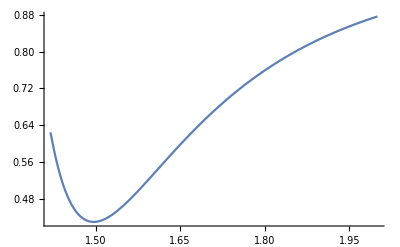

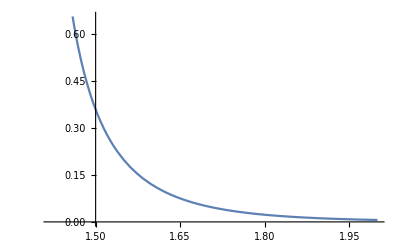

```mathematica
(* when x == y*)
z88x=1-3/((x^2-1)(x^4-1));
z38x=(z88x-1)*x/Sqrt[3];
zTox={Z88-> z88x,Z38->z38x,Z83->z38x};

tmp1=Simplify[trABABB/.zTox/.{y->x}]
tmp2a=Simplify[Coefficient[tmp1,Z33]]
tmp2b=Simplify[tmp1/.{Z33->0}]

z33x=Factor[(1-tmp2b)/tmp2a]

Simplify[z38x/.{x->Sqrt[2]}]
Simplify[z88x/.{x->Sqrt[2]}]
Simplify[z33x/.{x->Sqrt[2]}]

Simplify[z38x/.{x->Sqrt[3]}]
Simplify[z88x/.{x->Sqrt[3]}]
FullSimplify[z33x/.{x->Sqrt[3]}]

NMinimize[z88x^2+z38x^2,x]
Plot[{z88x^2+z38x^2},{x,1.42,2}]
Plot[{z33x^2+z38x^2},{x,1.42,2}]

ClearAll[z38xy,tmp1,z33,tmp2a,tmp2b];
```

```mathematica
ClearAll[Dist];
Dist[expected_List,a1_Real,a2_Real,a4_Real,a5_Real,a6_Real,a7_Real]:=Module[{Z,ret},
(*Print[{a1,a2,a4,a5,a6,a7}];*)
If[NumberQ[a1]==False,Return[100.0]];
(*Return[a1+a2+a4+a5+a6+a7];*)

Z=ExpF[N[{a1,a2,0,a4,a5,a6,a7,0}]];
ret = Abs[expected[[1]]-Z[[3,3]]]^2+Abs[expected[[2]]-Z[[3,8]]]^2+Abs[expected[[2]]-Z[[8,3]]]^2+Abs[expected[[3]]-Z[[8,8]]]^2;
(*Print[ret];*)
Return[ret];
];

ClearAll[FindABySearch];
FindABySearch[x_,z33_,z38_,z88_]:=Module[{res,A,alist,U,B},
res=FindMinimum[{Dist[{z33,z38,z88}, a1,a2,a4,a5,a6,a7], -2.0≤ a1 ≤ 2.0 && -2.0≤ a2 ≤ 2.0&&-2.0≤ a4 ≤ 2.0&&-2.0≤ a5 ≤ 2.0&&-2.0≤ a6 ≤ 2.0&&-2.0≤ a7 ≤ 2.0}, {{a1,1.0},{a2,1.0},{a4,0.0},{a5,0.0},{a6,-1.0},{a7,0.5}}];
Print["Search Result: ", res];
A=DiagonalMatrix[{x,-x,1}];
alist={a1,a2,0,a4,a5,a6,a7,0}/.res[[2]];
U=ExpGM[alist];
B=ConjugateTranspose[U].A.U;
Print["AABBB=",Tr[A.A.B.B.B], ", AAABB=",Tr[A.A.A.B.B], ", AAAAB=", Tr[A.A.A.A.B], ", ABBBB=", Tr[A.B.B.B.B] ];
Print["ABABB=",Tr[A.B.A.B.B], ", BABAA=",Tr[B.A.B.A.A] ];
Return[res]
];

FindABySearch[Sqrt[3.0], 71.0/1344, -3.0/16, 13.0/16]
Dist[{71.0/1344, -3.0/16, 13.0/16}, 1.0,2.0,1.0,2.3,3.0,4.0]
```

Search Result: {0.0174497,{a1→1.04554,a2→1.05061,a4→-0.822947,a5→-0.282704,a6→-2.29567×10^-6,a7→1.26578×10^-6}}

AABBB=0.0505161-1.53591×10^-15 ⅈ, AAABB=0.0505155-9.63963×10^-16 ⅈ, AAAAB=0.64074-4.996×10^-16 ⅈ, ABBBB=0.640739+3.2937×10^-15 ⅈ

ABABB=1.35402+7.8582×10^-16 ⅈ, BABAA=1.35402-2.71343×10^-15 ⅈ

{0.0174497,{a1→1.04554,a2→1.05061,a4→-0.822947,a5→-0.282704,a6→-2.29567×10^-6,a7→1.26578×10^-6}}

0.167963

```mathematica
On[Assert]
(*Assert[VerifyTrabcAll[]]*)

Assert[VerifyGM[]==True]
Assert[VerifyFsu3[]==True]
Assert[VerifyDsu3[]==True]
Assert[Table[TestTri8j3[i,j],{i,1,8},{j,1,8}]==ConstantArray[0,{8,8}]]
Assert[Table[TestTri8j8[i,j],{i,1,8},{j,1,8}]==ConstantArray[0,{8,8}]]
alist={1,4,2,3,2,2,-1,0};
Assert[Chop[Collect[TestTrUAAUB[alist],x]]==0]
Assert[Chop[Collect[TestTrUAAUB[ConstantArray[0,8]],x]]==0]

(*Chop[Collect[TestTrUAU8UAU1[alist],x]]
Chop[Collect[TestTrUAU8UAU1[ConstantArray[0,8]],x]]
Assert[Chop[Collect[TestY[alist],x]]==ConstantArray[0,{3,3}]]*)
(*Chop[Collect[TestTrY8[alist],x]]*)
(*Chop[Collect[TestTrUAU8UAU1b[alist],x]]*)

(*Chop[Collect[TestTrUAU8UAUB[alist],x]]
Chop[Collect[TestTrUAU8UAUB[ConstantArray[0,8]],x]]*)
Chop[Collect[TestTrABABB[alist],{x,y}]]
Chop[Collect[TestTrABABB[ConstantArray[0,8]],{x,y}]]

TestTrY3[alist]
TestTrY3[ConstantArray[0,8]]

TestTrY8[alist]
TestTrY8[ConstantArray[0,8]]

TestTrYB[alist]
TestTrYB[ConstantArray[0,8]]
VerifyExpF[alist];
```

res=0.379855+0.100787 y+0.236469 y^2+0.062742 y^3+x^2 (0.00641118-0.041 y+0.377265 y^2-0.122529 y^3)+x (0.0986979-0.574035 y-0.0986979 y^2+0.574035 y^3)

0

res=1.

0

0

0

«4 more identical outputs»

```mathematica
cxyn=Factor[cxy/.{y->x}]
Factor[cz33/.{y->x}];
Factor[%/(4/9*(x^2-1))]
Factor[(cz38+cz83)/.{y->x}];
cz38n=Factor[%/(4/9*(x^2-1))]
Factor[cz88/.{y->x}];
cz88n=Factor[%/(4/9*(x^2-1))]
Simplify[1/9 (1+2 x^2+6 x^4)+4/9(x^2-1)(-3/2x^2-2)]
Collect[-4x^2 Z38^2-2/3Z88^2+5x/Sqrt[3]Z38*Z88/.{Z38->(Z88-1)/Sqrt[3]x},Z88]
Factor[cz38n*(x/Sqrt[3])+cz88n]
Factor[-cz38n*(x/Sqrt[3])*4/9*(x^2-1)+cxyn]
Factor[%+2(x^2-1)/3*(-4/3x^2)]
Simplify[%/.{x->Sqrt[2]}]
```

1/9 (1+2 x^2+6 x^4)

x^2

1/2 √3 x (1+2 x^2)

1/6 (-8-3 x^2)

1

-(4 x^4)/3+(-(5 x^2)/3+(8 x^4)/3) Z88+(-2/3+(5 x^2)/3-(4 x^4)/3) Z88^2

1/3 (-4+3 x^4)

-1/9 (-1+2 x-4 x^2+2 x^3) (1+2 x+4 x^2+2 x^3)

1/9 (1+12 x^2-4 x^6)

-7/9

```mathematica
SoGenerator[n_,a_,b_]:=Module[{ret},
ret=ConstantArray[0,{n,n}];
ret[[a,b]]=-1;
ret[[b,a]]=1;
Return[ret]
];

L12=SoGenerator[4,1,2];
L23=SoGenerator[4,2,3];
L34=SoGenerator[4,3,4];
L13=SoGenerator[4,1,3];
L14=SoGenerator[4,1,4];
L24=SoGenerator[4,2,4];
```

```mathematica
z88=1+1/(y^2-1)-3x^2y^2/((y^2+1)(x^2-1));
TrigFactor[z88/.{x->Sin[c],y->Cos[c]/Sqrt[1+Sin[c]^2]}]
z83=-Sqrt[3]x^2/(y(y^2-1)(x^4-1));
TrigFactor[z83/.{x->Sin[c],y->Cos[c]/Sqrt[1+Sin[c]^2]}]
z38=-Sqrt[3]y^2/(x(x^2-1)(y^4-1));
TrigFactor[z38/.{x->Sin[c],y->Cos[c]/Sqrt[1+Sin[c]^2]}]
```

1/16 (5-16 Cos[2 c]+3 Cos[4 c]) Csc[c]^2

-1/2 √(3/2) √(3-Cos[2 c]) Sec[c]^3

1/8 √3 (-3+Cos[2 c]) Csc[c]^3

```mathematica
Sum[coefA[[i]]*Fsu3Mat[i],{i,1,8}]
```

{{0,a3,-a2,a7/2,-a6/2,a5/2,-a4/2,0},{-a3,0,a1,a6/2,a7/2,-a4/2,-a5/2,0},{a2,-a1,0,a5/2,-a4/2,-a7/2,a6/2,0},{-a7/2,-a6/2,-a5/2,0,a3/2+(√3 a8)/2,a2/2,a1/2,-(√3 a5)/2},{a6/2,-a7/2,a4/2,-a3/2-(√3 a8)/2,0,-a1/2,a2/2,(√3 a4)/2},{-a5/2,a4/2,a7/2,-a2/2,a1/2,0,-a3/2+(√3 a8)/2,-(√3 a7)/2},{a4/2,a5/2,-a6/2,-a1/2,-a2/2,a3/2-(√3 a8)/2,0,(√3 a6)/2},{0,0,0,(√3 a5)/2,-(√3 a4)/2,(√3 a7)/2,-(√3 a6)/2,0}}